Ground State energies:

max = 10 ; np = 100

pMin = 0 ;  pMax = 1.4 ;  R = 0.2

p = 0.359609

A m = 0.0651819

A l = 0.0651819

E = -6.46593

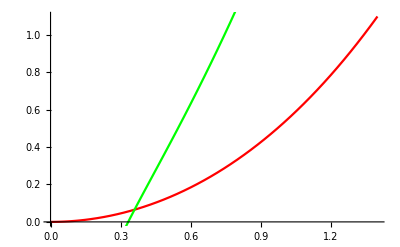

InterpolatingFunction::dmval: Input value {-0.14037} lies outside the range of data in the interpolating function. Extrapolation will be used.

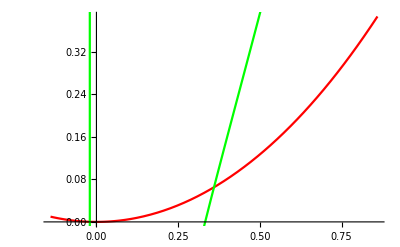

```mathematica
(* Matrix Dimensions *)
(* From HydrogenIon-2D-6.tex  *) 
max =10;

R = .2; 
d[m_,n_]:=KroneckerDelta[m,n];

mSumEven[m_,k_]:=(-4 k^2+p^2/2)d[m,k] +p^2/4 d[m,k+1]+ p^2/4 d[m,k-1];
mSumOdd[m_,k_]:=(-(2k+1)^2+p^2/4)d[m,k]+p^2/4 d[m,k+1]+ p^2/4 d[m,k-1];

(* M matrix *)
matrixMEven = Table[0,{i,1,max}];
matrixMOdd = Table[0,{i,1,max}];


Do[
matrixMOdd[[m+1]] = Table[mSumOdd[m,k], {k,0,max-1}];
matrixMEven[[m+1]] = Table[mSumEven[m,k], {k,0,max-1}],
{m,0,max-1}
]

matrixMEven[[1]][[2]] = 2matrixMEven[[1]][[2]];
matrixMOdd[[1]][[1]] = -1+p^2/4;

(* L Matrix *)
matrixL = Table[0,{i,1,max}];

lSum[m_,k_] := ((-2)p k(2k+1)-(2p-1)k^2-4p k +(2R-p)(2k+1)-p -p^2+2R)d[m,k]+(2p k(k+1)-(2R-p)(k+1))d[m,k+1]+(2p k^2+(2p-1)k(2k-1) +(4p-2)k -(2R-p)k)d[m,k-1] -(2p-1)k(k-1)d[m,k-2]+
Sum[d[m,i],{i,0,k-1}];

Do[
matrixL[[m+1]] = Table[(-1)lSum[m,k],{k,0,max-1}],
{m,0,max-1}
]

np =100;

pMax = 2R+1;
pMin = 0;
pStep = (pMax-pMin)/np;

pgrid = Table[pMin+(i-1)*pStep, {i,1,np}];


(*Output *)

(* {p, eigenvalue @ p } *) 
eigenM = Table[0, {i,1,np},{j,1,2}];
eigenL = Table[0, {i,1,np},{j,1,2}];


rmG[x_]:=If[Im[x] ≠ 0,10^99,x];
rmL[x_]:=If[Im[x] ≠ 0,-10^99,x];

(*
rmG[x_]:=Re[x];
rmL[x_]:=Re[x];
*)


(* energyState = 1 == Ground State, 2 == First Excited State, etc..
nucleiDistance = Distance between nuclei *)

(*
Do[
pval = N[pgrid[[i]]] ;
eigenM[[i]][[1]] =  pval ;
eigenL[[i]][[1]] =  pval;
eigenM[[i]][[2]] = Sort[Map[rmL,Eigenvalues[N[matrixMEven/.p-> pval]]], Greater][[1]];
eigenL[[i]][[2]] =Sort[Map[rmG,Eigenvalues[N[matrixL/.p->pval]] ]][[1]],
{i,1,np}
];
*)

Do[
pval = N[pgrid[[i]]] ;
eigenM[[i]][[1]] =  pval ;
eigenL[[i]][[1]] =  pval;
eigenM[[i]][[2]] = Sort[Map[rmL,Eigenvalues[N[matrixMEven/.p-> pval]]], Greater][[1]];
eigenL[[i]][[2]] =Sort[Map[rmG,Eigenvalues[N[matrixL/.p->pval]] ]][[1]],
{i,1,np}
];

 mFunc = (eigenM // Interpolation) ; 
lFunc  = (eigenL // Interpolation) ;

        (* value of p *)
If[R≥1,
pe =x /. FindRoot[mFunc[x] == lFunc[x],{x,R/2.}],
pe =x /. FindRoot[mFunc[x] == lFunc[x],{x,2R}]];

Print["Ground State energies:"]

(* value of A *)
a1= mFunc[pe];
a2= lFunc[pe];

Print["max = ",max," ; np = ", np]
Print["pMin = ",pMin," ;  pMax = ", pMax," ;  R = ",R]

Print["p = ",pe]

Print["A m = ",a1]
Print["A l = ",a2]

ee = -2(pe/R)^2;

Print["E = ", ee]

Show[Plot[mFunc[x],{x,0,pMax},AxesOrigin->{0,0},PlotStyle->Red],
Plot[lFunc[x],{x,0,pMax}, AxesOrigin->{0,0},PlotStyle->Green]]

Show[Plot[mFunc[x],{x,pe-.5,pe+.5},AxesOrigin->{0,0},PlotStyle->Red],
Plot[lFunc[x],{x,pe-.5,pe+.5}, AxesOrigin->{0,0},PlotStyle->Green]]
```